# ScalarQED

```mathematica
NotebookDirectory[]
```

/home/raj/C_SM/ToySMat1Loop/

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$model="ScalarQED";
```

```mathematica
<<GenAmp`
```

Patched 2 FeynArts models.

## Setup

```mathematica
$gaugerules={FAGaugeXi[S[1]]:> 1};
```

```mathematica
$ampconfigFCFAConvert={ChangeDimension->D,Contract->False,DropSumOver->False,FCFADiracChainJoin->True,FeynAmpDenominatorCombine->True,
FinalSubstitutions->{},InitialSubstitutions->{},List->False,LoopMomenta->{l},LorentzIndexNames->{},Prefactor->1,SMP->False,SUNFIndexNames->{},
SUNIndexNames->{},TransversePolarizationVectors->{},UndoChiralSplittings->False};
```

## Tadpoles (1->0)

## One Loop A->0

loading generic model file /home/raj/C_SM/ToySMat1Loop/models/ScalarQED/ScalarQED.gen

> $GenericMixing is OFF

generic model {./models/ScalarQED/ScalarQED} initialized

loading classes model file /home/raj/C_SM/ToySMat1Loop/models/ScalarQED/ScalarQED.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 3 vertices

> 5 counterterms of order 1

classes model {./models/ScalarQED/ScalarQED} initialized

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

> Top. 1 ab/0/bb.m, 0 diagrams

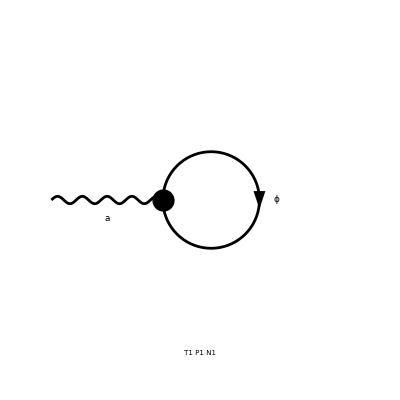

```mathematica
D1LA=diag[1,{V[1]},{}];
```

```mathematica
Amp1LA=D1LA//amp1L[{p1},{}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

in total: 0 Particles amplitudes

Part::partw: Part 2 of {} does not exist.

{(ⅈ e l^Lor1)/(8 π^4 (l^2-mP^2)),0}

```mathematica
Amp1LA//amp1LSimplify[{},{SMP["Delta"]}]
```

0

## One Loop (1->1)

## One Loop P->P

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 1 Particles insertion

in total: 3 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

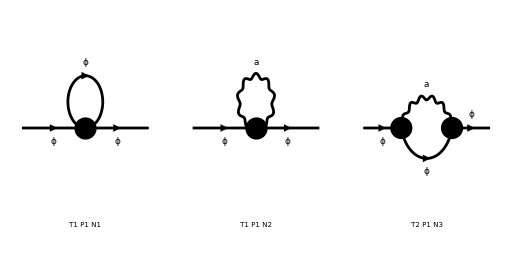

> Top. 1 ac/bc/0.m, 0 diagrams

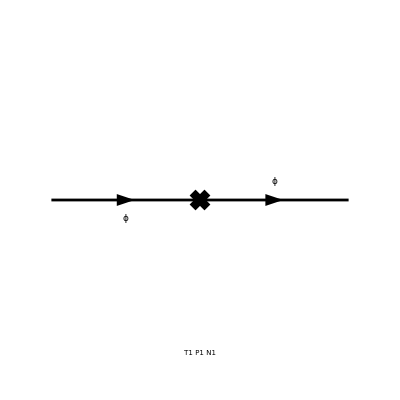

```mathematica
D1LPP=diag[1,{S[1]},{S[1]}];
```

```mathematica
Amp1LPP=D1LPP//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 1 Particles amplitude

in total: 3 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ (-ⅈ e l^Lor1-ⅈ e p1^Lor1) (-ⅈ e l^Lor2-ⅈ e p1^Lor2) (g^Lor1Lor2/((l^2-mP^2).(l-p1)^2)+((1-ξ_(V(1))) (l-p1)^Lor1 (p1-l)^Lor2)/((l^2-mP^2).((l-p1)^2)^2)))/(16 π^4)-(ⅈ g4)/(16 π^4 (l^2-mP^2))-(ⅈ e^2 g^Lor1Lor2 (g^Lor1Lor2/l^2-(l^Lor1 l^Lor2 (1-ξ_(V(1))))/((l^2)^2)))/(16 π^4),-ⅈ (ⅈ p1^2 (ZP-1)-ⅈ mP^2 (ZmP^2 ZP-1))}

```mathematica
Amp1LPPDiv=Amp1LPP//amp1LSimplify[{ZP:> 1+Nd dP,ZmP:> 1+Nd dmP},{SMP["Delta"],dP, dmP}]
```

-2 dmP mP^2-dP mP^2+dP p1^2+(Δ (e^2 (-mP^2) ξ_(V(1))+e^2 p1^2 ξ_(V(1))-3 e^2 p1^2+g4 mP^2))/(8 π^2)

```mathematica
dsol[1]=Solve[SelectNotFree2[Amp1LPPDiv,p1]==0,dP]//Flatten//Simplify
dSave[dsol[1]];
```

{dP→-(Δ e^2 (ξ_(V(1))-3))/(8 π^2)}

```mathematica
dsol[2]=Solve[SelectFree2[Amp1LPPDiv/.dSub[dmP],p1]==0,dmP]//Flatten//Simplify
dSave[dsol[2]];
```

{dmP→(Δ (g4-3 e^2))/(16 π^2)}

## One Loop A->A

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

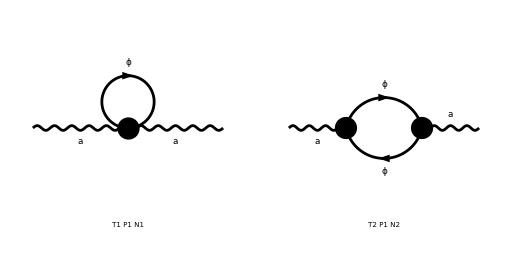

> Top. 1 ac/bc/0.m, 0 diagrams

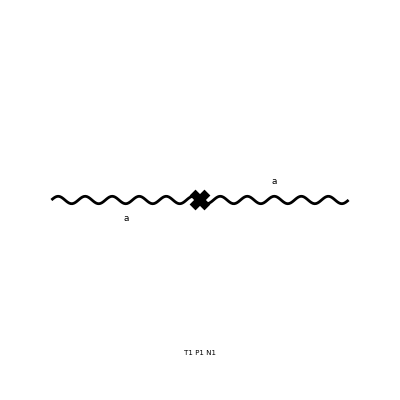

```mathematica
D1LAA=diag[1,{V[1]},{V[1]}];
```

```mathematica
Amp1LAA=D1LAA//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(ⅈ (ⅈ e (l-p1)^Lor1+ⅈ e l^Lor1) (ⅈ e l^Lor2-ⅈ e (p1-l)^Lor2))/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^2 g^Lor1Lor2)/(8 π^4 (l^2-mP^2)),-ⅈ (ⅈ (ZA-1) p1^Lor1 p1^Lor2-ⅈ p1^2 (ZA-1) g^Lor1Lor2)}

```mathematica
Amp1LAADiv=Amp1LAA//amp1LSimplify[{ZA:> 1+Nd dA},{SMP["Delta"],dA}]
```

dA (p1^Lor1 p1^Lor2-p1^2 g^Lor1Lor2)+(Δ e^2 (p1^Lor1 p1^Lor2-p1^2 g^Lor1Lor2))/(24 π^2)

```mathematica
dsol[3]=Solve[SelectNotFree2[Amp1LAADiv/.dSub[dA],{SMP["Delta"],dA}]==0,dA]//Flatten//Simplify
dSave[dsol[3]];
```

{dA→-(Δ e^2)/(24 π^2)}

## One Loop (2->1)

## One Loop SS->A

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 4 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 adbe/cf/dedfef.m, 0 diagrams

> Top. 2 adbe/ce/dede.m, 0 diagrams

> Top. 3 adbe/cd/eded.m, 0 diagrams

> Top. 4 adbd/ce/eded.m, 0 diagrams

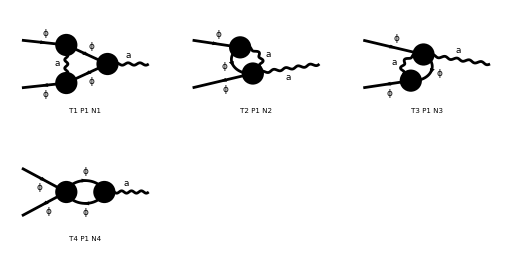

> Top. 1 adbd/cd/0.m, 0 diagrams

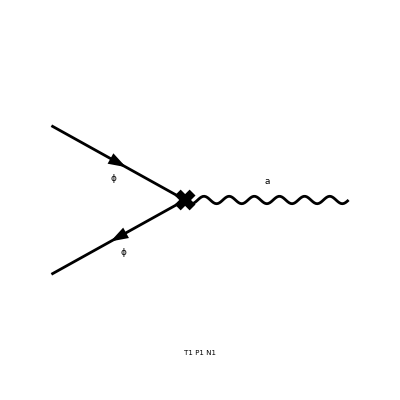

```mathematica
D1LPPA=diag[1,{S[1],-S[1]},{V[1]}];
```

```mathematica
Amp1LPPA=D1LPPA//amp1L[{p1,p2},{p1+p2}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

in total: 4 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(e^2 g^Lor1Lor3 (-ⅈ e l^Lor2-ⅈ e p1^Lor2) (g^Lor2Lor3/((l^2-mP^2).(l-p1)^2)+((1-ξ_(V(1))) (l-p1)^Lor2 (p1-l)^Lor3)/((l^2-mP^2).((l-p1)^2)^2)))/(8 π^4)+(e^2 g^Lor1Lor3 (ⅈ e l^Lor2+ⅈ e p2^Lor2) (g^Lor2Lor3/((l^2-mP^2).(l-p2)^2)+((1-ξ_(V(1))) (l-p2)^Lor2 (p2-l)^Lor3)/((l^2-mP^2).((l-p2)^2)^2)))/(8 π^4)+((ⅈ e (l-p1)^Lor2-ⅈ e p1^Lor2) (ⅈ e p2^Lor3-ⅈ e (-l-p2)^Lor3) (ⅈ e (l+p2)^Lor1-ⅈ e (p1-l)^Lor1) (g^Lor2Lor3/(l^2.((l+p2)^2-mP^2).((l-p1)^2-mP^2))-(l^Lor2 l^Lor3 (1-ξ_(V(1))))/((l^2)^2.((l+p2)^2-mP^2).((l-p1)^2-mP^2))))/(16 π^4)+(g4 (ⅈ e (l+p1+p2)^Lor1+ⅈ e l^Lor1))/(16 π^4 (l^2-mP^2).((l+p1+p2)^2-mP^2)),-ⅈ (ⅈ e p2^Lor1 (√ZA ZAPP ZP-1)-ⅈ e p1^Lor1 (√ZA ZAPP ZP-1))}

```mathematica
Amp1LPPADiv=Amp1LPPA//amp1LSimplify[{ZAPP:> 1+Nd dAPP,ZP:> 1+Nd dP,ZA:> 1+Nd dA},{SMP["Delta"],dAPP,dP,dA}]
```

-1/2 dA e (p1^Lor1-p2^Lor1)-dAPP e (p1^Lor1-p2^Lor1)-dP e (p1^Lor1-p2^Lor1)-(Δ e^3 (ξ_(V(1))-3) (p1^Lor1-p2^Lor1))/(8 π^2)

```mathematica
dsol[4]=Solve[SelectNotFree2[Amp1LPPADiv/.dSub[dAPP],{SMP["Delta"],dAPP}]==0,dAPP]//Flatten//Simplify
dSave[dsol[4]];
```

{dAPP→(Δ e^2)/(48 π^2)}

## One Loop (2->2)

## One Loop SS->SS

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

> Top. 5: 2 Particles insertions

> Top. 6: 1 Particles insertion

> Top. 7: 1 Particles insertion

> Top. 8: 1 Particles insertion

> Top. 9: 2 Particles insertions

> Top. 10: 1 Particles insertion

> Top. 11: 2 Particles insertions

> Top. 12: 2 Particles insertions

in total: 19 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/efef.m, 0 diagrams

> Top. 11 aebf/cedf/efef.m, 0 diagrams

> Top. 12 aebf/cfde/efef.m, 0 diagrams

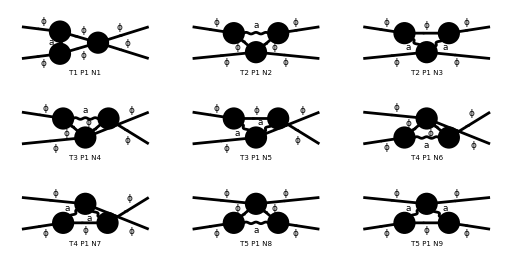

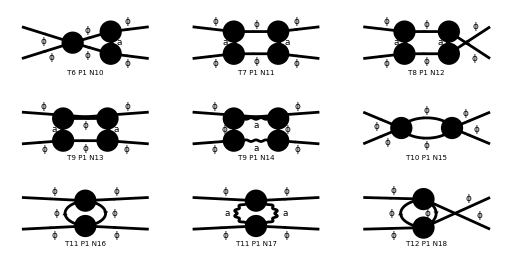

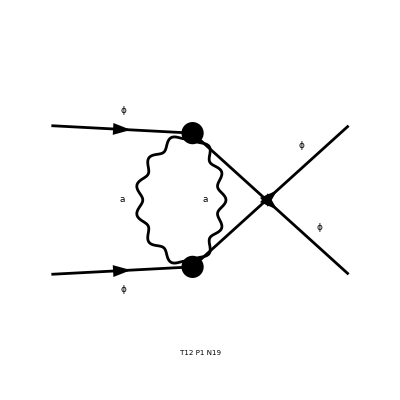

> Top. 1 aebe/cede/0.m, 0 diagrams

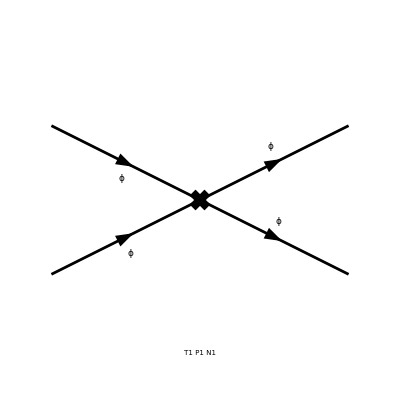

```mathematica
D1LPPPP=diag[1,{S[1],S[1]},{S[1],S[1]}];
```

```mathematica
Amp1LPPPP=D1LPPPP//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

> Top. 5: 2 Particles amplitudes

> Top. 6: 1 Particles amplitude

> Top. 7: 1 Particles amplitude

> Top. 8: 1 Particles amplitude

> Top. 9: 2 Particles amplitudes

> Top. 10: 1 Particles amplitude

> Top. 11: 2 Particles amplitudes

> Top. 12: 2 Particles amplitudes

in total: 19 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g^Lor1Lor3 g^Lor2Lor4 (((1-ξ_(V(1)))^2 l^Lor1 l^Lor2 l^Lor3 l^Lor4)/((l^2)^4)-((1-ξ_(V(1))) l^Lor1 l^Lor2 g^Lor3Lor4)/((l^2)^3)-((1-ξ_(V(1))) g^Lor1Lor2 l^Lor3 l^Lor4)/((l^2)^3)+(g^Lor1Lor2 g^Lor3Lor4)/((l^2)^2)) e^4)/(4 π^4)-(ⅈ (-ⅈ e l^Lor1-ⅈ e p1^Lor1) g^Lor2Lor4 (-ⅈ e l^Lor3-ⅈ e p1^Lor3) (((1-ξ_(V(1)))^2 (l-p1)^Lor1 (p1-l)^Lor2 (p1-l)^Lor3 (l-p1)^Lor4)/((l^2-mP^2).((l-p1)^2)^4)+((1-ξ_(V(1))) (l-p1)^Lor1 (p1-l)^Lor2 g^Lor3Lor4)/((l^2-mP^2).((l-p1)^2)^3)+((1-ξ_(V(1))) g^Lor1Lor2 (p1-l)^Lor3 (l-p1)^Lor4)/((l^2-mP^2).((l-p1)^2)^3)+(g^Lor1Lor2 g^Lor3Lor4)/((l^2-mP^2).((l-p1)^2)^2)) e^2)/(2 π^4)-(ⅈ g4^2)/(8 π^4 (l^2-mP^2)^2)-(ⅈ g4^2)/(32 π^4 (l^2-mP^2).((l-2 p1)^2-mP^2))-(ⅈ g4 (ⅈ e (l-p1)^Lor1-ⅈ e p1^Lor1) (g^Lor1Lor2/(l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-((1-ξ_(V(1))) l^Lor1 l^Lor2)/((l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))) (ⅈ e (-l-p1)^Lor2-ⅈ e p1^Lor2))/(16 π^4)-(ⅈ g4 (ⅈ e (l-p1)^Lor1-ⅈ e p1^Lor1) (g^Lor1Lor2/(l^2.((l-p1)^2-mP^2)^2)-((1-ξ_(V(1))) l^Lor1 l^Lor2)/((l^2)^2.((l-p1)^2-mP^2)^2)) (-ⅈ e p1^Lor2-ⅈ e (p1-l)^Lor2))/(4 π^4)-(ⅈ g4 (-ⅈ e p1^Lor1-ⅈ e (l+p1)^Lor1) (g^Lor1Lor2/(l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-((1-ξ_(V(1))) l^Lor1 l^Lor2)/((l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))) (-ⅈ e p1^Lor2-ⅈ e (p1-l)^Lor2))/(16 π^4)-1/(16 π^4)ⅈ (ⅈ e (l-p1)^Lor1-ⅈ e p1^Lor1) (-ⅈ e p1^Lor2-ⅈ e (p1-l)^Lor2) (ⅈ e (l-p1)^Lor3-ⅈ e p1^Lor3) (((1-ξ_(V(1)))^2 l^Lor1 l^Lor2 l^Lor3 l^Lor4)/((l^2)^2.((l-p1)^2-mP^2).(l^2)^2.((l-p1)^2-mP^2))-((1-ξ_(V(1))) l^Lor1 l^Lor2 g^Lor3Lor4)/((l^2)^2.((l-p1)^2-mP^2).l^2.((l-p1)^2-mP^2))-((1-ξ_(V(1))) g^Lor1Lor2 l^Lor3 l^Lor4)/(l^2.((l-p1)^2-mP^2).(l^2)^2.((l-p1)^2-mP^2))+(g^Lor1Lor2 g^Lor3Lor4)/(l^2.((l-p1)^2-mP^2).l^2.((l-p1)^2-mP^2))) (-ⅈ e p1^Lor4-ⅈ e (p1-l)^Lor4)-1/(16 π^4)ⅈ (ⅈ e (l-p1)^Lor1-ⅈ e p1^Lor1) (ⅈ e (-l-p1)^Lor2-ⅈ e p1^Lor2) (-ⅈ e p1^Lor3-ⅈ e (l+p1)^Lor3) (((1-ξ_(V(1)))^2 l^Lor1 l^Lor2 l^Lor3 l^Lor4)/((l^2)^2.((l+p1)^2-mP^2).(l^2)^2.((l-p1)^2-mP^2))-((1-ξ_(V(1))) l^Lor1 l^Lor2 g^Lor3Lor4)/((l^2)^2.((l+p1)^2-mP^2).l^2.((l-p1)^2-mP^2))-((1-ξ_(V(1))) g^Lor1Lor2 l^Lor3 l^Lor4)/(l^2.((l+p1)^2-mP^2).(l^2)^2.((l-p1)^2-mP^2))+(g^Lor1Lor2 g^Lor3Lor4)/(l^2.((l+p1)^2-mP^2).l^2.((l-p1)^2-mP^2))) (-ⅈ e p1^Lor4-ⅈ e (p1-l)^Lor4)-1/(16 π^4)ⅈ (-ⅈ e l^Lor1-ⅈ e p1^Lor1) (-ⅈ e l^Lor2-ⅈ e p1^Lor2) (-ⅈ e l^Lor3-ⅈ e p1^Lor3) (-ⅈ e l^Lor4-ⅈ e p1^Lor4) (((1-ξ_(V(1)))^2 (l-p1)^Lor1 (p1-l)^Lor2 (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-mP^2).((l-p1)^2)^2.(l^2-mP^2).((l-p1)^2)^2)+((1-ξ_(V(1))) (l-p1)^Lor1 (p1-l)^Lor2 g^Lor3Lor4)/((l^2-mP^2).(l-p1)^2.(l^2-mP^2).((l-p1)^2)^2)+((1-ξ_(V(1))) g^Lor1Lor2 (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-mP^2).((l-p1)^2)^2.(l^2-mP^2).(l-p1)^2)+(g^Lor1Lor2 g^Lor3Lor4)/((l^2-mP^2).(l-p1)^2.(l^2-mP^2).(l-p1)^2))-1/(16 π^4)ⅈ (ⅈ e (l-p1)^Lor1-ⅈ e p1^Lor1) (ⅈ e (-l-p1)^Lor2-ⅈ e p1^Lor2) (-ⅈ e p1^Lor3-ⅈ e (p1-l)^Lor3) (((1-ξ_(V(1)))^2 l^Lor1 l^Lor2 l^Lor3 l^Lor4)/((l^2)^2.((l+p1)^2-mP^2).(l^2)^2.((l-p1)^2-mP^2))-((1-ξ_(V(1))) l^Lor1 l^Lor2 g^Lor3Lor4)/((l^2)^2.((l+p1)^2-mP^2).l^2.((l-p1)^2-mP^2))-((1-ξ_(V(1))) g^Lor1Lor2 l^Lor3 l^Lor4)/(l^2.((l+p1)^2-mP^2).(l^2)^2.((l-p1)^2-mP^2))+(g^Lor1Lor2 g^Lor3Lor4)/(l^2.((l+p1)^2-mP^2).l^2.((l-p1)^2-mP^2))) (-ⅈ e p1^Lor4-ⅈ e (l+p1)^Lor4),-g4 (ZP^2 ZPPPP-1)}

```mathematica
Amp1LPPPPDiv=Amp1LPPPP//amp1LSimplify[{ZPPPP:> 1+Nd dPPPP,ZP:> 1+Nd dP},{SMP["Delta"],dPPPP,dP}]//Simplify
```

(Δ (24 e^4-4 e^2 g4 ξ_(V(1))+5 g4^2))/(16 π^2)-g4 (2 dP+dPPPP)

```mathematica
dsol[5]=Solve[SelectNotFree2[Amp1LPPPPDiv/.dSub[dPPPP],{SMP["Delta"],dPPPP}]==0,dPPPP]//Flatten//Simplify
dSave[dsol[5]];
```

{dPPPP→(Δ (24 e^4-12 e^2 g4+5 g4^2))/(16 π^2 g4)}

## One Loop SA->SA

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

> Top. 5: 2 Particles insertions

> Top. 6: 1 Particles insertion

> Top. 7: 1 Particles insertion

> Top. 8: 0 Particles insertions

> Top. 9: 1 Particles insertion

> Top. 10: 1 Particles insertion

> Top. 11: 1 Particles insertion

> Top. 12: 1 Particles insertion

in total: 12 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 9 aebe/cfdf/efef.m, 0 diagrams

> Top. 10 aebf/cedf/efef.m, 0 diagrams

> Top. 11 aebf/cfde/efef.m, 0 diagrams

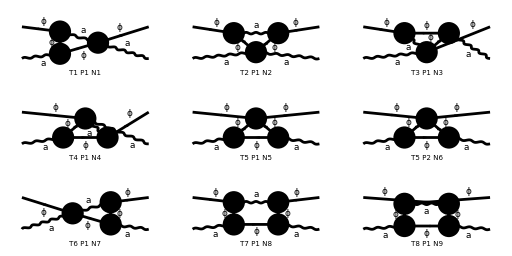

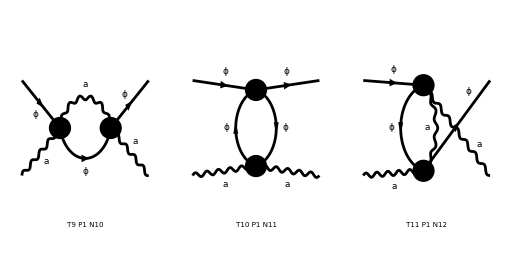

> Top. 1 aebe/cede/0.m, 0 diagrams

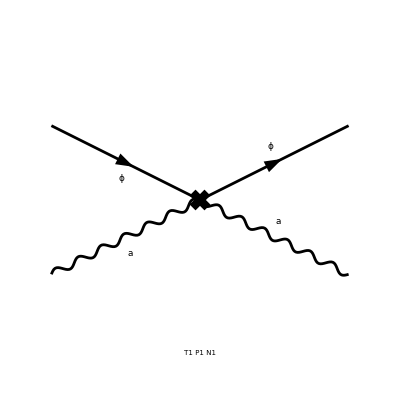

```mathematica
D1LPAPA=diag[1,{S[1],V[1]},{S[1],V[1]}];
```

```mathematica
Amp1LPAPA=D1LPAPA//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

> Top. 5: 2 Particles amplitudes

> Top. 6: 1 Particles amplitude

> Top. 7: 1 Particles amplitude

> Top. 8: 1 Particles amplitude

> Top. 9: 1 Particles amplitude

> Top. 10: 1 Particles amplitude

> Top. 11: 1 Particles amplitude

in total: 12 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(ⅈ g^Lor1Lor4 g^Lor2Lor3 (g^Lor3Lor4/((l^2-mP^2).l^2)-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2-mP^2).(l^2)^2)) e^4)/(4 π^4)+(ⅈ g^Lor1Lor3 g^Lor2Lor4 (g^Lor3Lor4/((l^2-mP^2).(l-2 p1)^2)+((1-ξ_(V(1))) (l-2 p1)^Lor3 (2 p1-l)^Lor4)/((l^2-mP^2).((l-2 p1)^2)^2)) e^4)/(4 π^4)+(ⅈ e^2 g4 g^Lor1Lor2)/(8 π^4 (l^2-mP^2)^2)+(ⅈ g^Lor1Lor4 (ⅈ e l^Lor2-ⅈ e (p1-l)^Lor2) (ⅈ e l^Lor3-ⅈ e p1^Lor3) (g^Lor3Lor4/((l^2-mP^2).(l+p1)^2.((l-p1)^2-mP^2))+((1-ξ_(V(1))) (l+p1)^Lor3 (-l-p1)^Lor4)/((l^2-mP^2).((l+p1)^2)^2.((l-p1)^2-mP^2))) e^2)/(8 π^4)+(ⅈ (-ⅈ e l^Lor1-ⅈ e (l-p1)^Lor1) g^Lor2Lor4 (-ⅈ e l^Lor3-ⅈ e p1^Lor3) (g^Lor3Lor4/((l^2-mP^2).((l-p1)^2-mP^2).(l-p1)^2)+((1-ξ_(V(1))) (p1-l)^Lor3 (l-p1)^Lor4)/((l^2-mP^2).((l-p1)^2-mP^2).((l-p1)^2)^2)) e^2)/(8 π^4)+(ⅈ g^Lor1Lor2 (ⅈ e (l-p1)^Lor3-ⅈ e p1^Lor3) (g^Lor3Lor4/(l^2.((l-p1)^2-mP^2)^2)-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2)^2.((l-p1)^2-mP^2)^2)) (-ⅈ e p1^Lor4-ⅈ e (p1-l)^Lor4) e^2)/(8 π^4)+(ⅈ g^Lor1Lor4 (ⅈ e (p1-l)^Lor2-ⅈ e l^Lor2) (-ⅈ e l^Lor3-ⅈ e p1^Lor3) (g^Lor3Lor4/((l^2-mP^2).((l-p1)^2-mP^2).(l-p1)^2)+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-mP^2).((l-p1)^2-mP^2).((l-p1)^2)^2)) e^2)/(8 π^4)+(ⅈ (ⅈ e (-l-p1)^Lor1-ⅈ e l^Lor1) g^Lor2Lor4 (-ⅈ e l^Lor3-ⅈ e p1^Lor3) (g^Lor3Lor4/((l^2-mP^2).((l+p1)^2-mP^2).(l-p1)^2)+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-mP^2).((l+p1)^2-mP^2).((l-p1)^2)^2)) e^2)/(8 π^4)+(ⅈ g4 (ⅈ e l^Lor1+ⅈ e (l-p1)^Lor1) (ⅈ e l^Lor2-ⅈ e (p1-l)^Lor2))/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2)^2)+(ⅈ g4 (-ⅈ e l^Lor1-ⅈ e (l-p1)^Lor1) (ⅈ e (p1-l)^Lor2-ⅈ e l^Lor2))/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2)^2)+(ⅈ (ⅈ e l^Lor1+ⅈ e (l-p1)^Lor1) (ⅈ e l^Lor2-ⅈ e (p1-l)^Lor2) (ⅈ e (l-p1)^Lor3-ⅈ e p1^Lor3) (g^Lor3Lor4/(l^2.((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2)^2.((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))) (-ⅈ e p1^Lor4-ⅈ e (p1-l)^Lor4))/(16 π^4)+(ⅈ (ⅈ e (-l-p1)^Lor1-ⅈ e l^Lor1) (-ⅈ e l^Lor2-ⅈ e (l+p1)^Lor2) (-ⅈ e l^Lor3-ⅈ e p1^Lor3) (-ⅈ e l^Lor4-ⅈ e p1^Lor4) (g^Lor3Lor4/((l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).(l-p1)^2)+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2)^2)))/(16 π^4),2 e^2 (ZA ZAAPP ZP-1) g^Lor1Lor2}

```mathematica
Amp1LPAPADiv=Amp1LPAPA//amp1LSimplify[{ZAAPP:> 1+Nd dAAPP,ZP:> 1+Nd dP,ZA:> 1+Nd dA},{SMP["Delta"],dAAPP,dP,dA}]//Simplify
```

(e^2 g^Lor1Lor2 (8 π^2 (dA+dAAPP+dP)+Δ e^2 (ξ_(V(1))-3)))/(4 π^2)

```mathematica
dsol[6]=Solve[SelectNotFree2[Amp1LPAPADiv/.dSub[dAAPP],{SMP["Delta"],dAAPP}]==0,dAAPP]//Flatten//Simplify
dSave[dsol[6]];
```

{dAAPP→(Δ e^2)/(24 π^2)}

## One Loop VV->VV

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

> Top. 5: 2 Particles insertions

> Top. 6: 2 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 2 Particles insertions

> Top. 9: 2 Particles insertions

> Top. 10: 1 Particles insertion

> Top. 11: 1 Particles insertion

> Top. 12: 1 Particles insertion

in total: 21 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/efef.m, 0 diagrams

> Top. 11 aebf/cedf/efef.m, 0 diagrams

> Top. 12 aebf/cfde/efef.m, 0 diagrams

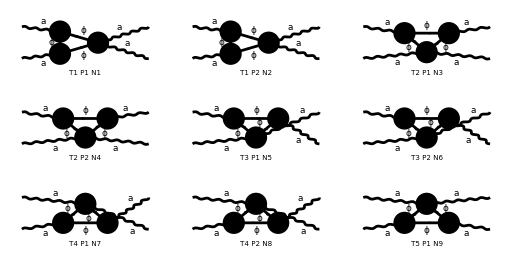

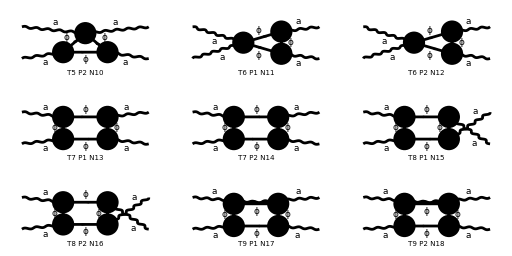

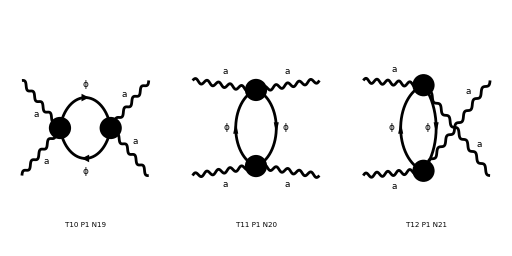

```mathematica
D1LAAAA=diag[1,{V[1],V[1]},{V[1],V[1]}];
```

```mathematica
Amp1LAAAA=D1LAAAA//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

> Top. 5: 2 Particles amplitudes

> Top. 6: 2 Particles amplitudes

> Top. 7: 2 Particles amplitudes

> Top. 8: 2 Particles amplitudes

> Top. 9: 2 Particles amplitudes

> Top. 10: 1 Particles amplitude

> Top. 11: 1 Particles amplitude

> Top. 12: 1 Particles amplitude

in total: 21 Particles amplitudes

creating amplitudes at level(s) {Particles}

in total: 0 Particles amplitudes

{-(ⅈ e^4 g^Lor1Lor4 g^Lor2Lor3)/(4 π^4 (l^2-mP^2)^2)-(ⅈ e^4 g^Lor1Lor3 g^Lor2Lor4)/(4 π^4 (l^2-mP^2)^2)-(ⅈ e^4 g^Lor1Lor2 g^Lor3Lor4)/(4 π^4 (l^2-mP^2).((l-2 p1)^2-mP^2))-(ⅈ e^2 (ⅈ e l^Lor1+ⅈ e (l-p1)^Lor1) (ⅈ e l^Lor2-ⅈ e (-l-p1)^Lor2) g^Lor3Lor4)/(8 π^4 (l^2-mP^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^2 (-ⅈ e l^Lor1-ⅈ e (l-p1)^Lor1) (ⅈ e (-l-p1)^Lor2-ⅈ e l^Lor2) g^Lor3Lor4)/(8 π^4 (l^2-mP^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^2 (ⅈ e l^Lor1+ⅈ e (l-p1)^Lor1) g^Lor2Lor4 (ⅈ e l^Lor3-ⅈ e (p1-l)^Lor3))/(8 π^4 (l^2-mP^2).((l-p1)^2-mP^2)^2)-(ⅈ e^2 g^Lor1Lor4 (ⅈ e l^Lor2+ⅈ e (l-p1)^Lor2) (ⅈ e l^Lor3-ⅈ e (p1-l)^Lor3))/(8 π^4 (l^2-mP^2).((l-p1)^2-mP^2)^2)-(ⅈ e^2 (-ⅈ e l^Lor1-ⅈ e (l-p1)^Lor1) g^Lor2Lor4 (ⅈ e (p1-l)^Lor3-ⅈ e l^Lor3))/(8 π^4 (l^2-mP^2).((l-p1)^2-mP^2)^2)-(ⅈ e^2 g^Lor1Lor4 (-ⅈ e l^Lor2-ⅈ e (l-p1)^Lor2) (ⅈ e (p1-l)^Lor3-ⅈ e l^Lor3))/(8 π^4 (l^2-mP^2).((l-p1)^2-mP^2)^2)-(ⅈ e^2 (ⅈ e l^Lor1+ⅈ e (l-p1)^Lor1) g^Lor2Lor3 (ⅈ e l^Lor4-ⅈ e (p1-l)^Lor4))/(8 π^4 (l^2-mP^2).((l-p1)^2-mP^2)^2)-(ⅈ e^2 g^Lor1Lor3 (ⅈ e l^Lor2+ⅈ e (l-p1)^Lor2) (ⅈ e l^Lor4-ⅈ e (p1-l)^Lor4))/(8 π^4 (l^2-mP^2).((l-p1)^2-mP^2)^2)-(ⅈ e^2 g^Lor1Lor2 (ⅈ e l^Lor3+ⅈ e (l+p1)^Lor3) (ⅈ e l^Lor4-ⅈ e (p1-l)^Lor4))/(8 π^4 (l^2-mP^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^2 (-ⅈ e l^Lor1-ⅈ e (l-p1)^Lor1) g^Lor2Lor3 (ⅈ e (p1-l)^Lor4-ⅈ e l^Lor4))/(8 π^4 (l^2-mP^2).((l-p1)^2-mP^2)^2)-(ⅈ e^2 g^Lor1Lor3 (-ⅈ e l^Lor2-ⅈ e (l-p1)^Lor2) (ⅈ e (p1-l)^Lor4-ⅈ e l^Lor4))/(8 π^4 (l^2-mP^2).((l-p1)^2-mP^2)^2)-(ⅈ e^2 g^Lor1Lor2 (-ⅈ e l^Lor3-ⅈ e (l+p1)^Lor3) (ⅈ e (p1-l)^Lor4-ⅈ e l^Lor4))/(8 π^4 (l^2-mP^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ (ⅈ e l^Lor1+ⅈ e (l-p1)^Lor1) (ⅈ e l^Lor2+ⅈ e (l-p1)^Lor2) (ⅈ e l^Lor3-ⅈ e (p1-l)^Lor3) (ⅈ e l^Lor4-ⅈ e (p1-l)^Lor4))/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ (ⅈ e l^Lor1+ⅈ e (l-p1)^Lor1) (ⅈ e l^Lor2-ⅈ e (-l-p1)^Lor2) (ⅈ e l^Lor3+ⅈ e (l+p1)^Lor3) (ⅈ e l^Lor4-ⅈ e (p1-l)^Lor4))/(16 π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ (-ⅈ e l^Lor1-ⅈ e (l-p1)^Lor1) (-ⅈ e l^Lor2-ⅈ e (l-p1)^Lor2) (ⅈ e (p1-l)^Lor3-ⅈ e l^Lor3) (ⅈ e (p1-l)^Lor4-ⅈ e l^Lor4))/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ (-ⅈ e l^Lor1-ⅈ e (l-p1)^Lor1) (ⅈ e (-l-p1)^Lor2-ⅈ e l^Lor2) (-ⅈ e l^Lor3-ⅈ e (l+p1)^Lor3) (ⅈ e (p1-l)^Lor4-ⅈ e l^Lor4))/(16 π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ (-ⅈ e l^Lor1-ⅈ e (l-p1)^Lor1) (ⅈ e (-l-p1)^Lor2-ⅈ e l^Lor2) (ⅈ e (p1-l)^Lor3-ⅈ e l^Lor3) (-ⅈ e l^Lor4-ⅈ e (l+p1)^Lor4))/(16 π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ (ⅈ e l^Lor1+ⅈ e (l-p1)^Lor1) (ⅈ e l^Lor2-ⅈ e (-l-p1)^Lor2) (ⅈ e l^Lor3-ⅈ e (p1-l)^Lor3) (ⅈ e l^Lor4+ⅈ e (l+p1)^Lor4))/(16 π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2)),0}

```mathematica
Amp1LAAAA//amp1LSimplify[{},{SMP["Delta"]}]
```

0

## Final answers

```mathematica
dvalues
```

{dP→-(Δ e^2 (ξ_(V(1))-3))/(8 π^2),dmP→(Δ (g4-3 e^2))/(16 π^2),dA→-(Δ e^2)/(24 π^2),dAPP→(Δ e^2)/(48 π^2),dPPPP→(Δ (24 e^4-12 e^2 g4+5 g4^2))/(16 π^2 g4),dAAPP→(Δ e^2)/(24 π^2)}